```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sandrews/SSA/software/Smoldyn/trunk/examples/S94_archive/Andrews_2016/surface diffusion

```mathematica
time=300
diffconst=100
binwidth=Pi/90
lowend=0
highend=Pi
radius=450
```

300

100

π/90

0

π

450

```mathematica
(* Everything below here should take care of itself *)
```

```mathematica
(* Define functions *)
```

```mathematica
gauss[x_,mu_,sigma_]:=1/(sigma*Sqrt[2*Pi])*Exp[-(x-mu)^2/(2*sigma^2)]
```

```mathematica
Assuming[s>0,Integrate[gauss[x,mu,s],{x,-Infinity,Infinity}]]
```

1

```mathematica
(* Theory for sphere distribution.  Result is eq. 7 from Ghosh_Sinha_2012. *)
spheretheory[theta_,sigma_]:=Sin[theta]/2*Sum[(2*l+1)*Exp[-l*(l+1)*sigma^2/2]*LegendreP[l,Cos[theta]],{l,0,30}]
```

```mathematica
(* Load and look at data *)
```

```mathematica
simdata=Import["hemisphereout.txt","CSV"];
```

```mathematica
simdata
```

{{300,2136,6427,10814,14896,18466,22155,25903,28832,31323,33775,36054,37282,38253,39500,39729,39886,39510,38815,38590,36748,36163,34170,32831,30602,28855,27208,25383,23124,21029,19256,17549,15921,14113,12736,11586,9929,8741,7762,6833,5993,4945,4465,3695,3055,2600,2216,1882,1494,1282,1078,840,727,569,503,382,291,221,212,146,110,89,68,61,48,24,39,16,16,17,11,5,3,2,3,2,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0},{300,2729,7938,12973,17916,22354,26419,30182,33342,35777,38091,39861,40575,40812,41020,40700,40018,38732,36736,35952,33826,31874,30044,28112,26143,24034,22265,20498,18908,17052,15791,14283,13108,11750,10508,9599,8716,7726,7008,6358,5821,5194,4771,4153,3797,3413,3016,2810,2529,2269,2071,1860,1646,1597,1391,1267,1124,1081,968,910,777,719,660,615,576,479,472,417,427,355,346,311,281,292,202,236,191,167,159,139,147,131,99,91,82,79,49,39,27,14,3}}

```mathematica
simdata1=Drop[simdata[[1]],1]
```

{2136,6427,10814,14896,18466,22155,25903,28832,31323,33775,36054,37282,38253,39500,39729,39886,39510,38815,38590,36748,36163,34170,32831,30602,28855,27208,25383,23124,21029,19256,17549,15921,14113,12736,11586,9929,8741,7762,6833,5993,4945,4465,3695,3055,2600,2216,1882,1494,1282,1078,840,727,569,503,382,291,221,212,146,110,89,68,61,48,24,39,16,16,17,11,5,3,2,3,2,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0}

```mathematica
simdata2=Drop[simdata[[2]],1]
```

{2729,7938,12973,17916,22354,26419,30182,33342,35777,38091,39861,40575,40812,41020,40700,40018,38732,36736,35952,33826,31874,30044,28112,26143,24034,22265,20498,18908,17052,15791,14283,13108,11750,10508,9599,8716,7726,7008,6358,5821,5194,4771,4153,3797,3413,3016,2810,2529,2269,2071,1860,1646,1597,1391,1267,1124,1081,968,910,777,719,660,615,576,479,472,417,427,355,346,311,281,292,202,236,191,167,159,139,147,131,99,91,82,79,49,39,27,14,3}

```mathematica
Length[simdata2]
```

90

```mathematica
nmolec=Total[simdata2]
Total[simdata1]
```

1000000

1000000

```mathematica
xvector=Table[i,{i,lowend+binwidth/2,highend-binwidth/2,binwidth}];
```

```mathematica
Length[xvector]
```

90

```mathematica
simdata1xy=Transpose[{xvector,simdata1}];
```

```mathematica
simdata2xy=Transpose[{xvector,simdata2}];
```

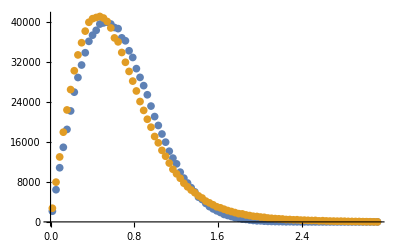

```mathematica
ListPlot[{simdata1xy,simdata2xy}]
```

```mathematica
sigma=N[Sqrt[2*time*diffconst]/radius]
```

0.544331

```mathematica
theoryfn[x_]:=nmolec*binwidth*spheretheory[x,sigma]
```

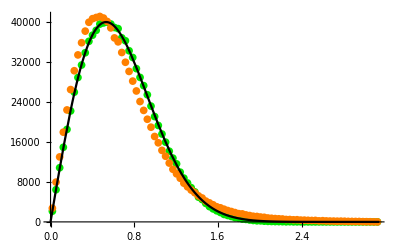

```mathematica
Show[{ListPlot[{simdata1xy,simdata2xy},PlotStyle->{RGBColor[0,0.9,0],Orange}],
Plot[theoryfn[x],{x,lowend,highend},PlotStyle->Black]},Axes->{True,False},AxesStyle->Bold,TicksStyle->Directive[FontOpacity->0,FontSize->1]]
```

```mathematica
errors1=Table[simdata1[[i]]-N[theoryfn[xvector[[i]]]],{i,1,Length[simdata1]}];
```

```mathematica
errors2=Table[simdata2[[i]]-N[theoryfn[xvector[[i]]]],{i,1,Length[simdata2]}];
```

```mathematica
StandardDeviation[errors1]
StandardDeviation[errors2]
```

126.748

2210.07

```mathematica
errors1xy=Transpose[{xvector,errors1}];
```

```mathematica
errors2xy=Transpose[{xvector,errors2}];
```

```mathematica
theoryerror[x_]=Sqrt[theoryfn[x]];
```

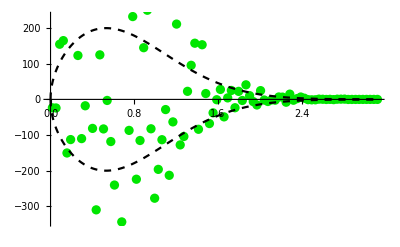

```mathematica
Show[{ListPlot[{errors1xy},PlotStyle->{RGBColor[0,0.9,0]}],Plot[theoryerror[x],{x,lowend,highend},PlotStyle->Directive[Black,Dashed]],Plot[-theoryerror[x],{x,lowend,highend},PlotStyle->Directive[Black,Dashed]]},Axes->{True,False},AxesStyle->Bold,TicksStyle->Directive[FontOpacity->0,FontSize->1]]
```